```mathematica
f[x_]:=(x-1)*(x-1.5)*(x-2.5)*(x-2)*(x-3)*(x-4)*(x-4.5)
```

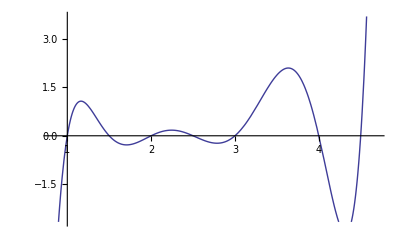

```mathematica
Plot[f[x],{x,0.8,4.8}]
```

```mathematica
Table[Plot[Exp[-f[x]/T],{x,0.8,4.8}],{T,1,20}]
```

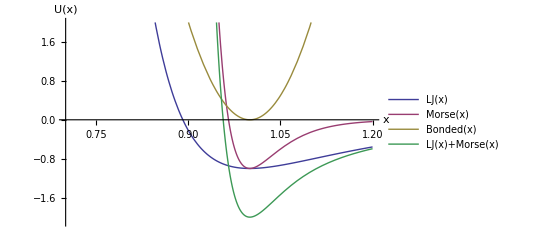

potentials.pdf

```mathematica
R=1;
epsilon=1;
LJ[x_]:=epsilon*((x/R)^-12-2*(x/R)^-6)
d=1;
alpha=20;
r0=1;
kappa=200;
Morse[x_]:=d*(1-Exp[-alpha*(Abs[x]-r0)])^2-d
Bonded[x_]:=kappa*(x-r0)^2;
Plot[{LJ[x],Morse[x],Bonded[x],LJ[x]+Morse[x]},{x,0.7,1.2},PlotRange->{{0.7,1.2},{-2.1,2}},AxesOrigin->{0.7,0},PlotStyle->Thick,PlotLegends->"Expressions",AxesLabel->{"x","U(x)"},LabelStyle->Directive[Bold,10]]
Export["potentials.pdf",%,"PDF"]
```